```mathematica
filesAR=FileNames["/home/carla/GDC/MUR/GDC_Conf_AR_MUR_DOJ_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/MUR/GDC_Conf_BR_MUR_DOJ_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{0.000584864,5,8549},{0.000584864,5,8549},{0.0555556,1,18},{0.0555556,1,18},{0.00980392,1,102},{0.00236407,1,423},{0.0833333,1,12},{1.,1,1}}

{{0.000584864,40,68392},{0.00038613,5,12949},{0.0555556,9,162},{0.0140845,1,71},{0.00410397,126,30702},{0.00236407,1,423},{0.25,9,36}}

```mathematica
dojAR=confAR[[All,1]]
dojBR=confBR[[All,1]]
```

{0.000584864,0.000584864,0.0555556,0.0555556,0.00980392,0.00236407,0.0833333,1.}

{0.000584864,0.00038613,0.0555556,0.0140845,0.00410397,0.00236407,0.25}

```mathematica
sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
```

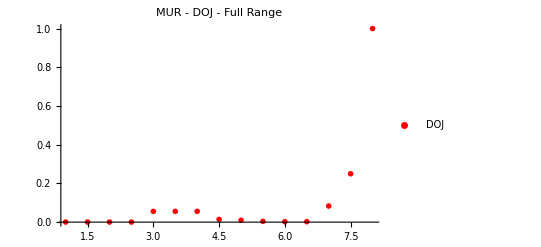

```mathematica
PlotDOJAllParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"MUR - DOJ - Full Range", PlotMarkers->{{"D",12}}]
```

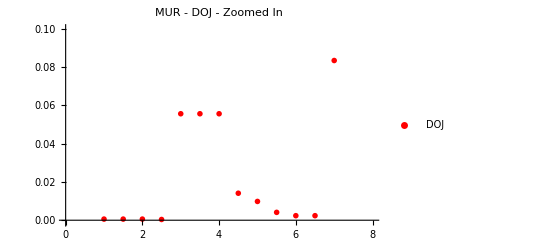

```mathematica
PlotDOJParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->{-0.001, 0.1},  PlotLabel->"MUR - DOJ - Zoomed In",  PlotMarkers->{{"D",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/MUR/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"MUR_DOJ.txt"]
Export["MUR_DOJ.jpeg",PlotDOJAllParts,ImageSize->850]
Export["MUR_DOJ_Zoomed_In.jpeg",PlotDOJParts,ImageSize->850]
```

MUR_DOJ.jpeg

MUR_DOJ_Zoomed_In.jpeg